```mathematica
ClearSystemCache[];
ClearAll[uniformPDF];
uniformPDF[
N1_, 
N2_, 
N3_,
N4_,
a1_, 
a2_, 
s_,
prec_]:= uniformPDF[N1, N2, N3, N4, a1, a2, s, prec] = (
in = NIntegrate[
1 * Boole[(N4 - N3 x - N2 y)^2 + (N3 - N2 x - N1 y)^2 < (N4 - N3 a1 - N2 a2)^2 + (N3 - N2 a1 - N1 a2)^2],
 {x, -1, 1}, {y, -1, 1},
WorkingPrecision->prec
];
s/4(1 - 1/4 Evaluate[in])^(s - 1)
)

 uniformPDF[33,95,74,85,-0.5, 0, 2, 6]
```

0.13469

```mathematica
ClearAll[pdf];
ClearAll[MeanVar];
meanVar[
N1_, 
N2_, 
N3_, 
N4_, 
s_, 
prec_,
pdf_] := meanVar[N1, N2, N3, N4, s, prec,pdf] = (
ea1 = NIntegrate[
a11 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s, prec]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea2 = NIntegrate[
a22 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s, prec]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea12 = NIntegrate[
a11^2 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s, prec]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
ea22 = NIntegrate[
a22^2 * Evaluate[pdf[N1, N2, N3, N4, a11, a22, s, prec]],
{a11, -1, 1},
{a22, -1, 1},
WorkingPrecision->prec
];
{ea1, ea2, Sqrt[ea12 - ea1^2], Sqrt[ea22 - ea2^2]}
)
meanVar[33,95,74,85, 2, 4, uniformPDF]
```

{0.2528,0.187,0.5092,0.5317}

```mathematica
ClearAll[barMap];
barMap[{N1_, N2_, N3_, N4_, s_, t_, n_, pdf_, prec_}] := barMap[{N1, N2, N3, N4, s, t, n,pdf, prec}] = (
topThreshold = Which[N4 > 0, (t- a22 N3)/N4, N4==0 , 1];
probGo = NIntegrate[
Evaluate[pdf[N1, N2, N3, N4, a11, a22, s, prec]],
{a22, -1, 1},
{a11, -1, Max[-1, Min[1,topThreshold]]},
WorkingPrecision->prec
];

{N2, N3, N4, n* probGo, s, t, n,pdf, prec}
)
barMap[{33,95,74,85, 2, 60, 100, uniformPDF, 8}]
```

NIntegrate::inumr: The integrand Boole[(85-74 x-95 y)^2+(74-95 x-33 y)^2<(85-74 a11-95 a22)^2+(74-95 a11-33 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{95,74,85,65.524277,2,60,100,uniformPDF,8}

```mathematica
Clear[fourth]
fourth[ll_] := fourth[ll] = ll[[4]];

ClearAll[runMap];
runMap[N1_, N2_, N3_, N4_, s_, t_, n_, iter_,pdf_,  prec_] := runMap[N1, N2, N3, N4, s, t, n, iter, pdf, prec] = (
maps = Reap[Nest[(Sow[barMap[#]])&, {N1,N2, N3, N4,s, t, n, pdf,prec},iter]];
fourth/@ maps[[2,1]]
)

runMap[33,95,74,85, 2, 60, 100, 30, uniformPDF, 3]
```

NIntegrate::inumr: The integrand Boole[(85-74 x-95 y)^2+(74-95 x-33 y)^2<(85-74 a11-95 a22)^2+(74-95 a11-33 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{65.7,69.3,75.8,69.8,69.5,72.5,71.,70.3,71.5,71.1,70.7,71.1,71.1,70.9,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.,71.}

```mathematica
runMap[33,95,74,85, 3, 60, 100, 30, uniformPDF, 8]
```

NIntegrate::inumr: The integrand Boole[(85-74 x-95 y)^2+(74-95 x-33 y)^2<(85-74 a11-95 a22)^2+(74-95 a11-33 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{53.771176,66.765363,80.991287,56.676476,64.065577,79.258591,58.784331,62.801427,78.013975,60.285734,62.261927,76.902903,61.387839,62.105584,75.872352,62.23454,62.159673,74.904961,62.907868,62.297942,74.021133,63.347991,62.552328,73.227514,63.864908,62.789745,72.425997,64.285424,63.059283,71.708294}

```mathematica
runMap[33,95,74,85, 5 60, 100, 30, uniformPDF, 8]
```

runMap[33,95,74,85,300,100,30,uniformPDF,8]

```mathematica
runMap[33,95,74,85, 10, 60, 100, 30, uniformPDF, 6]
```

NIntegrate::inumr: The integrand Boole[(85-74 x-95 y)^2+(74-95 x-33 y)^2<(85-74 a11-95 a22)^2+(74-95 a11-33 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{15.8058,62.8661,99.8402,10.6527,97.8548,98.9267,7.09387,99.3836,99.4788,7.01296,99.4833,99.4819,7.01266,99.4854,99.4822,7.01245,99.4854,99.4816,7.01245,99.4855,99.4823,7.01254,99.4856,99.4818,7.01254,99.4857,99.4822,7.01253,99.4851,99.4819}

```mathematica
runMap[33,95,74,85, 2, 60, 100, 30, uniformPDF, 10]
```

NIntegrate::inumr: The integrand Boole[(85-74 x-95 y)^2+(74-95 x-33 y)^2<(85-74 a11-95 a22)^2+(74-95 a11-33 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{65.51473342,69.13874901,75.99333966,69.98157505,69.46600256,72.56883669,71.21132001,70.33590183,71.42008112,71.31134849,70.82390019,71.11351313,71.21565976,71.01891874,71.06573246,71.14153491,71.08028667,71.07199483,71.10762054,71.09411084,71.08315811,71.09531623,71.09476484,71.08898241,71.09211996,71.09344775,71.09122759,71.09166503,71.0925545,71.09189633}

So it looks like there is a stable fixed point only at s=2.  What happens when we start at the fixed point.  Will we stay there?

```mathematica
fp = 60 / 0.8485760192680928
runMap[fp, fp, fp, fp, 2, 60, 100, 30, uniformPDF, 12]
```

70.7067

NIntegrate::inumr: The integrand Boole[2 (70.7067-70.7067 x-70.7067 y)^2<2 (70.7067-70.7067 a11-70.7067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.3375921116,71.0801196159,70.957938581,71.1563722255,71.1251908251,71.0436008083,71.1001652994,71.1128117614,71.0784513894,71.0892654678,71.1009783629,71.0897782296,71.0895236178,71.0952186298,71.0925135236,71.0910269037,71.093110925,71.0928138868,71.0919253918,71.0925148192,71.0926635143,71.0922965212,71.0924050555,71.09253356,71.0924157056,71.0924104099,71.0924716394,71.0924438296,71.0924272134,71.0924493017}

Now, what happens if we start a little above the fixed point?

```mathematica
runMap[fp+.1, fp + .1, fp + .1, fp + .1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (70.8067-70.8067 x-70.8067 y)^2<2 (70.8067-70.8067 a11-70.8067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.2736709626,71.0834195247,70.9927715654,71.1397148804,71.1165735903,71.056237112,71.0982197852,71.1074980818,71.0820618406,71.0901111015,71.0987615744,71.0904594032,71.0902867019,71.094500337,71.0924911534,71.0913950914,71.0929389613,71.0927163093,71.0920593978,71.0924967044,71.0926058915,71.0923341765,71.0924149829,71.0925099019,71.0924225322,71.0924187784,71.0924640845,71.0924434251,71.0924311708,71.0924475353}

```mathematica
runMap[fp-.1, fp - .1, fp - .1, fp - .1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (70.6067-70.6067 x-70.6067 y)^2<2 (70.6067-70.6067 a11-70.6067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.3975986487,71.0781160465,70.92411148,71.171823985,71.1336881082,71.0314808466,71.10188228,71.1180003714,71.0750164066,71.0883967606,71.1031198362,71.0891462734,71.0887736433,71.0959060044,71.0925447763,71.0906696903,71.0932730227,71.0929109172,71.0917965651,71.0925306317,71.0927197072,71.0922607218,71.0923949164,71.0925564008,71.0924093907,71.0924021934,71.0924788645,71.0924443226,71.092423376,71.0924509645}

```mathematica
runMap[fp, fp , fp , fp + .1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(70.7067-70.7067 x-70.7067 y)^2+(70.8067-70.7067 x-70.7067 y)^2<(70.7067-70.7067 a11-70.7067 a22)^2+(70.8067-«18» a11-70.7067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.2965896771,71.0608576551,70.9892434868,71.1513989126,71.1121003993,71.0526399468,71.1021936146,71.1073076,71.0801783133,71.0911419353,71.099185571,71.0897361534,71.0904355264,71.0947859927,71.0922751482,71.091360474,71.0930635764,71.092671566,71.0920196879,71.0925386948,71.0926047583,71.0923138628,71.0924256463,71.0925147001,71.092414845,71.0924202148,71.0924671924,71.0924411656,71.0924307489,71.0924488684}

```mathematica
runMap[fp, fp , fp , fp - .1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(70.6067-70.7067 x-70.7067 y)^2+(70.7067-70.7067 x-70.7067 y)^2<(70.6067-70.7067 a11-70.7067 a22)^2+(70.7067-«18» a11-70.7067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.3784960809,71.0994468643,70.9267152228,71.1613005334,71.1380500879,71.0346886303,71.0981713778,71.1182668943,71.0767335629,71.0874122966,71.102755755,71.0898168257,71.088621267,71.0956483213,71.0927486454,71.0906964333,71.0931583566,71.0929546294,71.0918318409,71.0924913588,71.0927216939,71.0922792601,71.0923847114,71.0925522573,71.0924165246,71.0924007065,71.0924760567,71.0924464579,71.0924237103,71.0924497366}

```mathematica
runMap[fp, fp , fp  + .1, fp , 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(70.7067-70.8067 x-70.7067 y)^2+(70.8067-70.7067 x-70.7067 y)^2<(70.7067-70.8067 a11-70.7067 a22)^2+(70.8067-«18» a11-70.7067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.3003359903,71.1040831948,70.9660040761,71.1410343174,71.1288085575,71.0494552866,71.0954622431,71.1122392239,71.0810728545,71.088246269,71.1001809779,71.090681149,71.0894709865,71.0947957597,71.0927499028,71.0911195989,71.0929472989,71.0928491475,71.0919892108,71.0924655562,71.0926562761,71.0923246129,71.0923946872,71.0925247478,71.092425242,71.0924100498,71.092467077,71.0924462771,71.092428265,71.092447562}

```mathematica
runMap[fp, fp , fp  - .1, fp , 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(70.6067-70.7067 x-70.7067 y)^2+(70.7067-70.6067 x-70.7067 y)^2<(70.6067-70.7067 a11-70.7067 a22)^2+(70.7067-«17» a11-70.7067 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

Was the fixed point RIGHT here?  Something looks off.

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < 1 - x + Abs[1 - a1 - a2] && y >  1 - x - Abs[1 - a1 - a2]],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)
pdfSameN[0.7,0.7,2]
```

0.4

```mathematica
ClearAll[res2];
res2 = Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1},
 Assumptions->r > 0
 ]
 sol2 = Solve[res2 == (.6)/r]
```

Piecewise[{{1, r≥2}, {1/24 (6+12 r+3 r^2-2 r^3), r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), True}}]

{{r→0.843971}}

```mathematica
fp = ((60 / r)/.sol2)[[1]]
```

71.0925

```mathematica
runMap[fp, fp, fp, fp, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (71.0925-71.0925 x-71.0925 y)^2<2 (71.0925-71.0925 a11-71.0925 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.0923859406,71.0924452111,71.0924737937,71.092427609,71.0924348248,71.0924538336,71.0924406224,71.0924376909,71.0924456969,71.0924431677,71.0924404422,71.0924430541,71.0924431103,71.0924417835,71.0924424152,71.0924427608,71.0924422749,71.0924423447,71.0924425516,71.0924424139,71.0924423795,71.0924424651,71.0924424396,71.0924424098,71.0924424373,71.0924424385,71.0924424242,71.0924424306,71.0924424346,71.0924424294}

```mathematica
runMap[fp, fp, fp, fp+0.1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(71.0925-71.0925 x-71.0925 y)^2+(71.1925-71.0925 x-71.0925 y)^2<(71.0925-71.0925 a11-71.0925 a22)^2+(71.1925-«18» a11-71.0925 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.0518377955,71.0727792593,71.1242103416,71.0874972255,71.0793754942,71.1015231694,71.0944615381,71.0869395244,71.094179648,71.094316861,71.0906475228,71.0924031866,71.0933544957,71.0920085225,71.0922047148,71.0927763694,71.0923945953,71.0923001843,71.0925369395,71.0924661671,71.0923836407,71.0924598597,71.092462996,71.0924235409,71.0924415982,71.0924522372,71.0924379695,71.0924397736,71.0924459705,71.0924419925}

```mathematica
runMap[fp, fp, fp, fp-0.1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(70.9925-71.0925 x-71.0925 y)^2+(71.0925-71.0925 x-71.0925 y)^2<(70.9925-71.0925 a11-71.0925 a22)^2+(71.0925-«18» a11-71.0925 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.1330406695,71.1120662967,71.0608597575,71.0973545051,71.1054687881,71.0834120186,71.0904256409,71.0979233372,71.0907166286,71.0905742602,71.0942290297,71.0924829006,71.09153402,71.0928739654,71.0926795397,71.0921099905,71.0924898302,71.092584154,71.0923484016,71.092418718,71.0925009721,71.092425115,71.092421934,71.0924612314,71.0924432746,71.0924326641,71.0924468676,71.0924450813,71.0924389074,71.0924428653}

```mathematica
runMap[fp+.1, fp+.1, fp+.1, fp+0.1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (71.1925-71.1925 x-71.1925 y)^2<2 (71.1925-71.1925 a11-71.1925 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.029202875,71.095513545,71.1275505082,71.0758865866,71.0839170559,71.1052023421,71.0904282712,71.0871356309,71.0960944453,71.0932697785,71.0902170167,71.0931381529,71.0932032387,71.0917183527,71.0924242038,71.0928115198,71.0922679926,71.0923456543,71.092577279,71.0924235033,71.0923847963,71.0924804974,71.0924521605,71.0924186672,71.0924494087,71.092450777,71.0924348122,71.0924420695,71.0924463988,71.092440638}

```mathematica
runMap[fp-.1, fp-.1, fp-.1, fp-0.1, 2, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (70.9925-70.9925 x-70.9925 y)^2<2 (70.9925-70.9925 a11-70.9925 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{71.1557079901,71.0893531296,71.0575539787,71.1089556728,71.1009208019,71.0797483421,71.0944559308,71.0977223381,71.0888065171,71.0916216121,71.0946572919,71.0917489767,71.0916859072,71.09316333,71.0924601428,71.0920752007,71.0926162102,71.0925386162,71.0923082074,71.0924613434,71.0924997636,71.0924045228,71.0924327732,71.0924660806,71.0924354745,71.0924341313,71.0924500164,71.0924427863,71.092438483,71.0924442173}

```mathematica
ClearAll[res3];
res3 = Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1},
 Assumptions->r > 0
 ]
 sol3 = Solve[res3 == (.6)/r]
```

Piecewise[{{1, r≥2}, {1/64 (8+24 r+18 r^2-3 r^4), r≤1}, {1/64 (-72+216 r-126 r^2+32 r^3-3 r^4), True}}]

{{r→-2.05308},{r→0.904798}}

```mathematica
fp3 = ((60 / r)/.sol3)[[2]]
```

66.3131

```mathematica
runMap[fp3, fp3, fp3, fp3, 3, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[2 (66.3131-66.3131 x-66.3131 y)^2<2 (66.3131-66.3131 a11-66.3131 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{66.3125368152,66.312999918,66.3130320251,66.3125592145,66.3129401824,66.3130167529,66.3126003197,66.3129061872,66.3130051205,66.3126392909,66.312880422,66.3129927562,66.312673513,66.3128605651,66.3129797592,66.3127031659,66.3128454946,66.3129666014,66.3127286606,66.3128343349,66.3129536676,66.3127504234,66.3128263461,66.312941238,66.3127688683,66.3128209003,66.3129295062,66.3127843865,66.3128174694,66.3129185958}

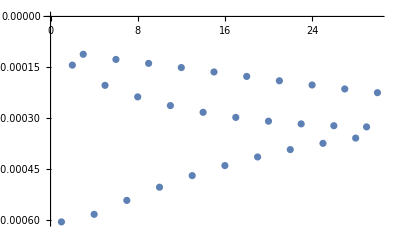

```mathematica
ListPlot[{66.31253681522978896810807699564910989019`12.,66.31299991803049648103100326910940909584`12.,66.31303202514066648838768250482743516594`12.,66.3125592145252918435626331777925873782`12.,66.31294018242351301250381010923325478017`12.,66.31301675294310468851159822813181623711`12.,66.31260031971292832136953111868865207153`12.,66.31290618720139658055346953541638750235`12.,66.31300512053247119756302304888302935026`12.,66.31263929089336251634158234646544641336`12.,66.3128804220214486944656774581907416349`12.,66.31299275624200082888752319024445948916`12.,66.31267351297670549090068709726248251941`12.,66.31286056512296847875000641500408477346`12.,66.31297975924486799194032705958879195352`12.,66.31270316591767607615192702243332952484`12.,66.31284549457717494906443574561829155033`12.,66.31296660138267463482684445639430952806`12.,66.3127286605539765310385306842209594023`12.,66.3128343348933135857621550113451685742`12.,66.31295366756918264191651445299776702657`12.,66.31275042342162870657515268030699223759`12.,66.31282634605357255747505983037485030825`12.,66.31294123804275069822840200893473892714`12.,66.31276886831647540937896097639831142776`12.,66.31282090029759475059703498606082887808`12.,66.31292950617891737819778165050227759548`12.,66.31278438646845909292373143046731144014`12.,66.31281746937016711741726822021917178393`12.,66.31291859581232588365158361485607888445`12.} - fp3]
```

```mathematica
runMap[fp3, fp3, fp3, fp3+0.1, 3, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(66.3131-66.3131 x-66.3131 y)^2+(66.4131-66.3131 x-66.3131 y)^2<(66.3131-66.3131 a11-66.3131 a22)^2+(66.4131-«18» a11-66.3131 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{66.2364956828,66.3075403658,66.3910410141,66.2501127849,66.3001660367,66.3816581146,66.2625717703,66.2964117662,66.3732633925,66.2733095651,66.2941900533,66.365509735,66.2822811215,66.2930631605,66.3584044388,66.2897011415,66.2927597302,66.351963464,66.2957835687,66.2929897224,66.3462411798,66.3007262805,66.2936793396,66.3411444418,66.3047034579,66.2946814697,66.3366413961,66.3078646114,66.2958867177,66.3326934139}

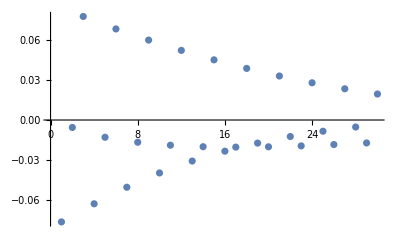

```mathematica
ListPlot[{66.23649568280861575468018073795809114982`12.,66.30754036580563011448780018133675267284`12.,66.39104101407817132772028888394689991867`12.,66.25011278488603289002076328513551012311`12.,66.30016603670982830589352850141613003823`12.,66.38165811463233308354675000994127325123`12.,66.26257177029911137926511829813710713927`12.,66.29641176620462478791987345521161713556`12.,66.37326339252843301458165498752211306021`12.,66.27330956509881333744724707443286211073`12.,66.29419005332699882923510216399146462474`12.,66.36550973502223179395660718419881061055`12.,66.28228112150131408466340580389879898035`12.,66.29306316047960206592998423314822919314`12.,66.35840443876942411858759374477929864942`12.,66.28970114147057157814282666016755447391`12.,66.29275973023940481334137036309378631979`12.,66.35196346400297410270896852066132126561`12.,66.29578356869382165917147598464489528377`12.,66.29298972240618572078121295651684194531`12.,66.34624117978049316738333407058374454025`12.,66.30072628049541202984074804327374410922`12.,66.29367933959621046611654787254714682032`12.,66.34114444183558286945092978489374992249`12.,66.30470345785690041628721160595798667069`12.,66.29468146967486210216151339241935975682`12.,66.33664139608999648345611441343789527547`12.,66.30786461138202673643858624027948171343`12.,66.29588671774615489597101922255030617675`12.,66.33269341394066708541557030394613080331`12.} - fp3]
```

```mathematica
runMap[fp3, fp3, fp3, fp3-0.1, 3, 60, 100, 30, uniformPDF, 12]
```

NIntegrate::inumr: The integrand Boole[(66.2131-66.3131 x-66.3131 y)^2+(66.3131-66.3131 x-66.3131 y)^2<(66.2131-66.3131 a11-66.3131 a22)^2+(66.3131-«18» a11-66.3131 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{66.3889755063,66.3181785631,66.2353298088,66.3754215008,66.3255150323,66.2445783783,66.3631303759,66.3291519087,66.2528055943,66.3525102667,66.3313838131,66.2604968756,66.3435665397,66.3325354126,66.2675202671,66.3361812016,66.3328627219,66.2738798621,66.3301355954,66.3325792864,66.2795842698,66.3251483574,66.3319166276,66.2846641492,66.3211451173,66.3308239818,66.289242067,66.3179702397,66.3295505709,66.2932510857}

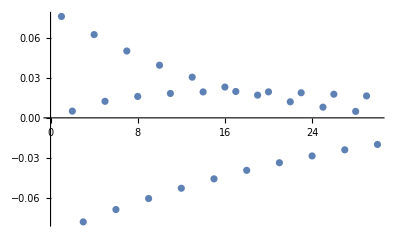

```mathematica
ListPlot[{66.3889755062708374807543505052522134138`12.,66.31817856311585116888078313348213861469`12.,66.23532980882798639016621479378294929537`12.,66.37542150078848319501129463585835874306`12.,66.32551503226826879886053710665606939626`12.,66.24457837832660555392042964852627611631`12.,66.36313037586697278124673835356507058613`12.,66.32915190867370139625538962111066798078`12.,66.25280559428363267537823372381772830585`12.,66.35251026665240045367044652223392538688`12.,66.33138381313631821494677954611374612202`12.,66.26049687563024905281086997502940128014`12.,66.34356653968792822702080904405259133458`12.,66.33253541257463192539232190305094686474`12.,66.26752026705856387523975794389484556967`12.,66.33618120164506955746024623134584040617`12.,66.33286272185920422771574193746169763345`12.,66.27387986207196010267710594295968090485`12.,66.33013559538273289347987477477731001062`12.,66.33257928637906325213060578843633026935`12.,66.27958426982371452165108498195369714091`12.,66.3251483574428804647718501265695438253`12.,66.33191662764062840249948507643149256201`12.,66.28466414922962126595209940060758100711`12.,66.32114511726576984150571468951143968762`12.,66.33082398181696718141387817149781350709`12.,66.28924206695716043985532694416704098589`12.,66.31797023970457084501928914117997649595`12.,66.3295505708657519725925898139389744185`12.,66.29325108568860814811338522607916549131`12.} - fp3]
```

```mathematica
runMap[fp3-0.1, fp3-0.1, fp3-0.1, fp3-0.1, 3, 60, 100, 30, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[2 (66.2131-66.2131 x-66.2131 y)^2<2 (66.2131-66.2131 a11-66.2131 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{66.4107521,66.2579815,66.2493827,66.402482,66.2777028,66.2537705,66.3890727,66.2890363,66.2572542,66.3763346,66.2976611,66.2610889,66.3651155,66.304313,66.2652096,66.3553699,66.3093601,66.2694405,66.3469763,66.3130925,66.2736396,66.3398039,66.3157566,66.2777026,66.3337231,66.3175629,66.2815562,66.3286092,66.3186885,66.2851522}

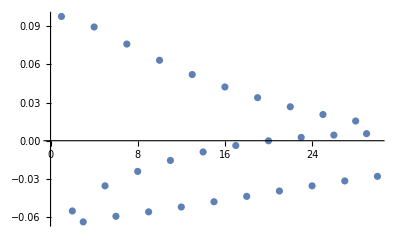

```mathematica
ListPlot[{66.4107521064966762941`9.,66.2579815491577946455`9.,66.2493826977798846674`9.,66.4024820005809312553`9.,66.2777027683999994418`9.,66.2537704767441656311`9.,66.3890726778648832072`9.,66.2890363193500109799`9.,66.2572542115604485897`9.,66.3763345816052461061`9.,66.2976610850999208764`9.,66.2610888907319072285`9.,66.3651155170466433152`9.,66.3043129897498806195`9.,66.2652095821215144722`9.,66.3553699233554405881`9.,66.309360134574281512`9.,66.2694404748995225364`9.,66.3469763163465368764`9.,66.3130924720865266582`9.,66.2736396031287628588`9.,66.3398039251029757819`9.,66.3157566381326735237`9.,66.2777026148750722523`9.,66.3337230757470679523`9.,66.3175628612231527707`9.,66.281556167116277838`9.,66.3286091584803396749`9.,66.3186884953685133726`9.,66.2851522248606793701`9.} - fp3]
```

```mathematica
runMap[fp3-0.1, fp3+0.1, fp3+0.1, fp3-0.1, 3, 60, 100, 30, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[(66.2131-66.4131 x-66.4131 y)^2+(66.4131-66.4131 x-66.2131 y)^2<(66.2131-66.4131 a11-66.4131 a22)^2+(66.4131-«18» a11-66.2131 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{66.3343859,66.392337,66.220418,66.3220899,66.3816867,66.2354796,66.3151166,66.3731208,66.2488533,66.3088474,66.3663103,66.2602939,66.3038661,66.360289,66.2700571,66.3004386,66.3545194,66.278322,66.2981764,66.3490791,66.2852523,66.2968284,66.3440251,66.2910142,66.2961888,66.3393904,66.2957617,66.2960872,66.3351886,66.2996357}

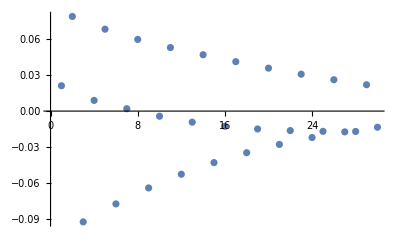

```mathematica
ListPlot[{66.3343859105360686532`9.,66.3923370205041523415`9.,66.2204179811820560844`9.,66.3220898791411066187`9.,66.3816867441931025536`9.,66.2354795563515253711`9.,66.3151166457456988767`9.,66.3731208160075980454`9.,66.2488533027388648957`9.,66.3088473677982926334`9.,66.3663103384980007063`9.,66.2602939485923144922`9.,66.3038660699425217305`9.,66.3602889939504738477`9.,66.2700570915553024542`9.,66.3004386471376201337`9.,66.3545193667371337501`9.,66.2783219861366492721`9.,66.2981764313746164681`9.,66.3490791324773688522`9.,66.2852523114083127934`9.,66.2968283665224029043`9.,66.3440251016481461258`9.,66.2910142390848871523`9.,66.2961887619813746428`9.,66.3393904048735481708`9.,66.2957617384245610022`9.,66.2960872060384982058`9.,66.3351886379678212661`9.,66.2996357254803385557`9.} - fp3]
```

```mathematica
runMap[64.1, 62.5, 71.5, 64.4, 3, 60, 100, 30, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[(71.5-62.5 x-64.1 y)^2+(64.4-71.5 x-62.5 y)^2<(71.5-62.5 a11-64.1 a22)^2+(64.4-71.5 a11-62.5 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{63.4518672,70.9630217,64.8500311,63.6932751,70.4049002,65.1486007,63.9034184,69.8485148,65.4222749,64.1124544,69.3317812,65.6696497,64.3177917,68.859277,65.8854289,64.5149484,68.4393246,66.066551,64.7022909,68.0717208,66.214712,64.8793557,67.7510388,66.5859215,64.8630453,67.4555684,66.9238161,64.8315449,67.1790244,67.2539783}

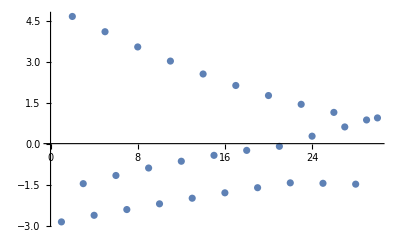

```mathematica
ListPlot[{63.451867246094704187`9.,70.9630216832909559003`9.,64.850031058227866073`9.,63.6932750933867526763`9.,70.4049001661626160358`9.,65.1486006930717094629`9.,63.9034184046440905541`9.,69.8485147789426339033`9.,65.4222749086706707473`9.,64.1124543906053354818`9.,69.3317812152982401058`9.,65.6696497402166265206`9.,64.3177916965327437198`9.,68.8592770387208200523`9.,65.8854288596313474036`9.,64.5149483906754794447`9.,68.439324636686429894`9.,66.0665510101077592354`9.,64.7022909096691708748`9.,68.0717208262451572303`9.,66.2147120063343666357`9.,64.8793556822675520095`9.,67.7510387973433212186`9.,66.5859214916599581862`9.,64.86304531243558797`9.,67.4555684243252072746`9.,66.9238161304417119137`9.,64.8315448846868767126`9.,67.1790243865039177142`9.,67.2539782818696700974`9.} - fp3]
```

```mathematica
ClearAll[res4];
res4 = Integrate[
 pdfSameN[x0, y0, 4] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1},
 Assumptions->r > 0
 ]
 sol4 = Solve[res4 == (.6)/r]
```

Piecewise[{{1, r≥2}, {1/160 (10+40 r+50 r^2+20 r^3-5 r^4-4 r^5), r≤1}, {1/160 (-408+1080 r-810 r^2+300 r^3-55 r^4+4 r^5), True}}]

{{r→0.942185}}

```mathematica
fp4 = 60/r/.sol4[[1]]
```

63.6817

```mathematica
runMap[fp4, fp4, fp4, fp4, 4, 60, 100, 40, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[(63.6967476-63.6379069 x-63.708783 y)^2+(63.7130847-63.6967476 x-63.6379069 y)^2<(63.6967476-63.6379069 a11-63.708783 a22)^2+(63.7130847-63.6967476 a11-63.6379069 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{63.6766779,63.6826544,63.6804129,63.6750356,63.6851023,63.6786767,63.6736903,63.6890921,63.6750111,63.6732021,63.6946865,63.6681051,63.6749651,63.7016455,63.6563285,63.6814765,63.708783,63.6379069,63.6967476,63.7130847,63.6115029,63.7266992,63.7083883,63.5774629,63.7792858,63.6835741,63.5401085,63.8638908,63.6204086,63.5115379,63.9887242,63.4914217,63.5180642,64.1566845,63.2571921,63.604067,64.3605028,62.875058,63.8305243,64.5784384}

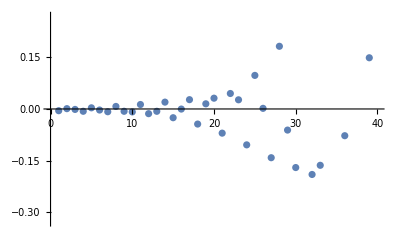

```mathematica
ListPlot[{63.6766778968821723565`9.,63.6826544200400371134`9.,63.6804128836770514689`9.,63.6750355702832770369`9.,63.6851023441563623691`9.,63.6786766679984963472`9.,63.6736902841616780131`9.,63.6890920523082254947`9.,63.6750111218979684795`9.,63.6732020898512791744`9.,63.6946865087159093345`9.,63.6681050569804946125`9.,63.6749651128806429018`9.,63.701645542599918639`9.,63.6563284563485444728`9.,63.6814764916436268458`9.,63.7087829783501630241`9.,63.6379068965148554334`9.,63.69674761033817655`9.,63.7130846634484408351`9.,63.611502859634597016`9.,63.7266992341156051651`9.,63.7083882600477487666`9.,63.5774629347393579971`9.,63.7792858433787435656`9.,63.6835740650289221264`9.,63.54010850301038669`9.,63.8638907743197116235`9.,63.6204086378949069914`9.,63.5115379035924960461`9.,63.9887241638656725274`9.,63.4914217433544086878`9.,63.5180641762011961816`9.,64.1566844907083998033`9.,63.2571920621091895033`9.,63.6040669533165611187`9.,64.3605027757091111864`9.,62.8750579793296512335`9.,63.8305243410302926689`9.,64.5784384139493890437`9.} - fp4]
```

```mathematica
ClearAll[res5];
res5 = Integrate[
 pdfSameN[x0, y0, 5] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1},
 Assumptions->r > 0
 ]
 sol5 = Solve[res5 == (.6)/r]
```

Piecewise[{{1, r≥2}, {1/384 (12+60 r+105 r^2+80 r^3+15 r^4-12 r^5-5 r^6), r≤1}, {1/384 (-1804+4860 r-4455 r^2+2160 r^3-585 r^4+84 r^5-5 r^6), True}}]

{{r→-2.31937},{r→0.965365}}

```mathematica
fp5 = (60/r )/.sol5[[2]]
```

62.1527

```mathematica
runMap[fp5, fp5, fp5, fp5, 5, 60, 100, 40, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[2 (62.1527-62.1527 x-62.1527 y)^2<2 (62.1527-62.1527 a11-62.1527 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{62.1517497,62.1532504,62.1519538,62.1515196,62.1546322,62.1496869,62.1530647,62.1558908,62.144528,62.1602249,62.1521648,62.1382858,62.1785016,62.1300377,62.1455355,62.2056511,62.0640018,62.2168382,62.1917626,61.958858,62.436143,61.9866423,61.9399243,62.8531981,61.2736227,62.4910338,63.1659473,59.7708069,64.8108447,61.8516178,58.1375529,70.5380069,55.5759116,58.8508172,79.7939542,43.9597412,61.1978716,90.5823136,35.6449973,63.4873431}

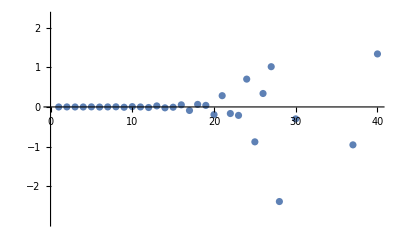

```mathematica
ListPlot[{62.1517496722952898249`9.,62.1532504398925855478`9.,62.1519538444808855625`9.,62.1515196337238336449`9.,62.1546322269515442072`9.,62.1496869024555875034`9.,62.1530647092187172394`9.,62.1558907610252017761`9.,62.1445279899195629307`9.,62.1602248930162703015`9.,62.1521648455203635489`9.,62.1382857587095120276`9.,62.178501626457513958`9.,62.1300376885212427783`9.,62.1455355392278698272`9.,62.2056510772158532268`9.,62.0640017579068250814`9.,62.2168382292625862405`9.,62.191762634785059449`9.,61.9588579879855059552`9.,62.4361430179596585508`9.,61.9866423390533703404`9.,61.939924321954054786`9.,62.8531981406091671204`9.,61.2736227444923944798`9.,62.4910337901609770541`9.,63.1659473312002301825`9.,59.770806935762597667`9.,64.8108447354932778268`9.,61.8516178372546686771`9.,58.1375529098381082626`9.,70.5380068736285940412`9.,55.5759116458807927964`9.,58.8508172424900101081`9.,79.7939541801163433783`9.,43.9597411752977343434`9.,61.1978715856162490232`9.,90.5823135651345411024`9.,35.6449972591971786875`9.,63.4873430889834722008`9.} - fp5]
```

```mathematica
runMap[fp5, fp5, fp5, fp5+0.1, 5, 60, 100, 40, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[(62.1527-62.1527 x-62.1527 y)^2+(62.2527-62.1527 x-62.1527 y)^2<(62.1527-62.1527 a11-62.1527 a22)^2+(62.2527-62.1527 a11-62.1527 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{61.9844364,62.3008283,62.1889651,61.8172777,62.7005903,61.7669089,61.8533124,63.4227112,60.4296186,63.0091299,63.8368574,57.8213944,67.3152641,61.2746826,55.2056389,76.7784926,51.9261626,54.5400333,89.5379555,39.8791674,53.1598773,97.7571006,35.3163621,53.9905164,98.7435442,34.8382482,57.5141942,98.0022122,34.0541701,63.3589543,96.2416568,33.0855802,73.8849103,91.5204071,32.0950353,81.748643,88.4424683,31.0199985,85.7572753,87.6257779}

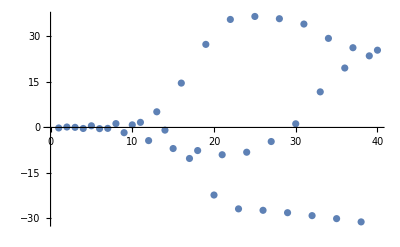

```mathematica
ListPlot[{61.9844364056576757594`9.,62.3008282930380324959`9.,62.188965148273373624`9.,61.8172776581153205898`9.,62.7005902730883643917`9.,61.7669088680626185265`9.,61.8533123668534519141`9.,63.4227111863114492122`9.,60.429618640274356694`9.,63.009129935347927263`9.,63.8368573549023757144`9.,57.8213943970103426157`9.,67.3152640982363284277`9.,61.2746825803180329272`9.,55.2056389060237155219`9.,76.7784926201227040945`9.,51.92616258409736741`9.,54.5400333005583045655`9.,89.5379554987119711466`9.,39.8791673994397233337`9.,53.1598772886135349628`9.,97.7571005945965380878`9.,35.3163621077043122641`9.,53.9905163543027447992`9.,98.7435441989438550847`9.,34.8382482282794812682`9.,57.5141942429070804257`9.,98.0022122101903563475`9.,34.0541701053676053605`9.,63.358954304192194719`9.,96.241656790534998848`9.,33.0855801797021345447`9.,73.8849102913081866935`9.,91.520407065750036124`9.,32.0950353070799497632`9.,81.748642970126060884`9.,88.4424682791750646255`9.,31.0199984969667095103`9.,85.7572752818192855534`9.,87.6257778971728412882`9.} - fp5]
```

```mathematica
runMap[fp5, fp5-0.1, fp5, fp5, 5, 60, 100, 40, uniformPDF, 9]
```

NIntegrate::inumr: The integrand Boole[(62.1527-62.0527 x-62.1527 y)^2+(62.1527-62.1527 x-62.0527 y)^2<(62.1527-62.0527 a11-62.1527 a22)^2+(62.1527-62.1527 a11-62.0527 a22)^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{62.0818759,62.2334798,62.1068786,62.0738209,62.3728897,61.8792413,62.2422605,62.481208,61.3918061,62.9544524,62.0873839,60.8404303,64.7994121,59.8706548,61.5197896,67.8172177,54.1582442,66.15522,70.0762506,46.0998166,76.8259432,69.2452033,39.1279931,88.4313414,70.3798418,33.8956108,93.0818911,77.572101,30.7696414,91.9153908,84.1658471,29.5466861,89.888274,87.135066,29.3678623,88.7866457,88.0131275,29.4357628,88.3717051,88.1614783}

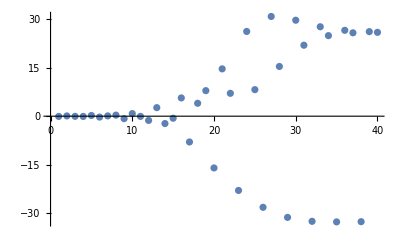

```mathematica
ListPlot[{62.0818758668887131014`9.,62.2334797953747674104`9.,62.1068785703623339007`9.,62.0738209171188503514`9.,62.3728897409018270381`9.,61.8792412884850559582`9.,62.2422604570719936832`9.,62.4812080439986425871`9.,61.3918061037563139541`9.,62.9544523612799852602`9.,62.0873838702707963536`9.,60.8404303254272887502`9.,64.7994121409152961473`9.,59.8706547586286568722`9.,61.5197895903048214681`9.,67.8172177176238003893`9.,54.1582441896816683187`9.,66.1552199572432803151`9.,70.0762506156559114221`9.,46.099816570635702474`9.,76.8259431710451936659`9.,69.2452032527652010013`9.,39.1279931372630648866`9.,88.4313413757386562904`9.,70.3798417850690810811`9.,33.8956107522621534131`9.,93.0818911372109443546`9.,77.5721010431180436288`9.,30.7696414029665876158`9.,91.9153908180321386253`9.,84.1658471368714135275`9.,29.5466861294508743635`9.,89.8882739748326782103`9.,87.1350659984727467363`9.,29.3678623240135271448`9.,88.786645689043617799`9.,88.0131274586031368465`9.,29.4357627732266731902`9.,88.3717050581597444146`9.,88.1614783351988931331`9.} - fp5]
```

```mathematica
ClearAll[res10];
res10 = Integrate[
 pdfSameN[x0, y0, 10] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1},
 Assumptions->r > 0
 ]
 sol10 = Solve[res10 == (.6)/r]
```

Piecewise[{{1, r≥2}, {(22+220 r+935 r^2+2310 r^3+3630 r^4+3696 r^5+2310 r^6+660 r^7-165 r^8-220 r^9-77 r^10-10 r^11)/22528, r≤1}, {(-1099404+4330260 r-7577955 r^2+7938810 r^3-5533110 r^4+2694384 r^5-935550 r^6+231660 r^7-40095 r^8+4620 r^9-319 r^10+10 r^11)/22528, True}}]

{{r→1.00297}}